```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.1; Ω = 0.4;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - Cos[β t]),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
alphaMasInterp = Interpolation[Table[{t, alphaMas[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaMenosInterp = Interpolation[Table[{t, alphaMenos[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaZInterp = Interpolation[Table[{t,alphaZ[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

PROBABILIDAD TRANSICIÓN

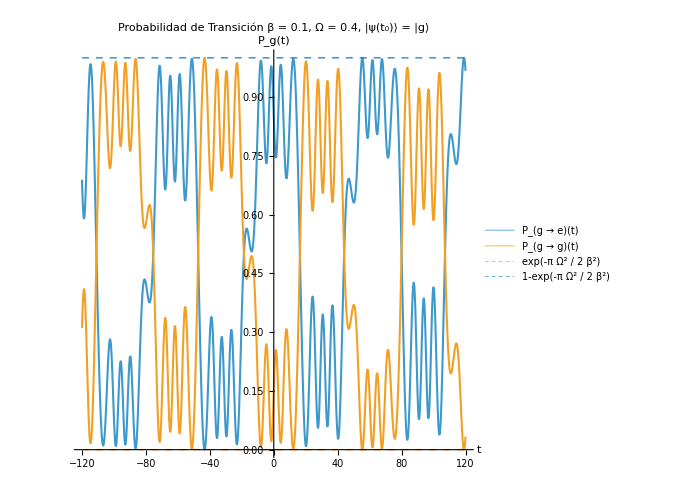

```mathematica
Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -120, 120}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.1, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

ENERGY LEVELS

```mathematica
del[T_]:= Cos[β T];
```

```mathematica
Ω^2/(2 β^2)
```

8.

```mathematica
Emas[T_, Ω_]:=1/2 Sqrt[Ω^2 +del[T]^2]
```

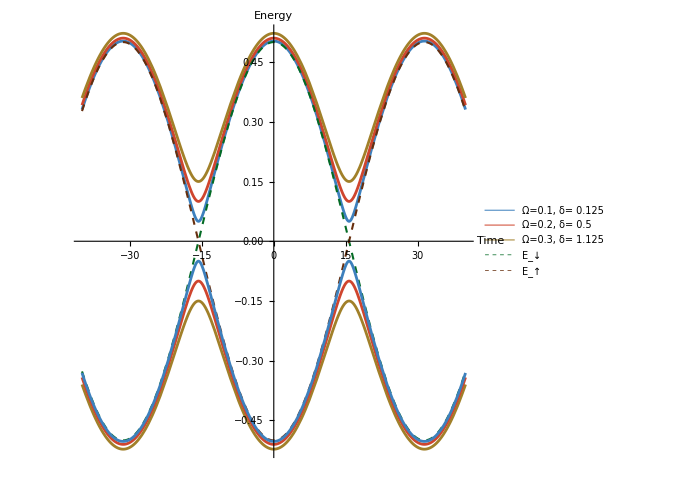

```mathematica
Plot[{Emas[t, 0.1],Emas[t, 0.2] ,Emas[t, 0.3],1/2 del[t],-1/2 del[t], -Emas[t,0.3],-Emas[t,0.2], -Emas[t,0.1]}, {t, -40, 40}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]],Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]],Directive[Thickness[0.003], Dashed, RGBColor[0.01,0.42,0.14]],Directive[Thickness[0.003], Dashed, RGBColor[0.4,0.18,0.05]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]] ,
Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]]},
PlotLegends->{Style["Ω=0.1, δ= 0.125"], Style["Ω=0.2, δ= 0.5"], Style["Ω=0.3, δ= 1.125"] , Style["E_↓",RGBColor[0.01,0.42,0.14] ],Style["E_↑",RGBColor[0.4,0.18,0.05] ] },
AxesLabel-> {Style["Time",16,GrayLevel[0.26]] , Style["Energy",16, GrayLevel[0.26]]}, AspectRatio->1, ImageSize->500]
```

INTEGRALES

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]]alphaMenosInterp[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZInterp[t]]alphaMenosInterp[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
NumEW3Periodic[Γ_,ν_,Δ_,to_,T_]:=2Γ Exp[-2 Γ T]*(Abs[NIntegrate[Exp[(Γ -I Δ )t+I (1/ν) Sin[ν t]],{t,to,T}]]^2)
```

```mathematica
T0=-220;T = -20;Γ = 0.1;ν=1.6; Ωr = Sqrt[ (T*β^2)^2+ Ω^2];
```

```mathematica
ωmin = (ν-1.6)/ν;ωmax = (ν+1.6)/ν;
```

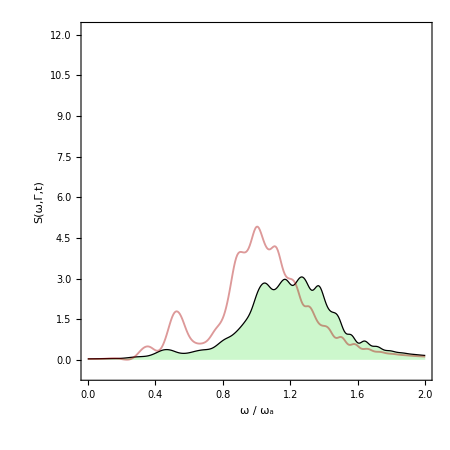

```mathematica
G1 =Show[{ListLinePlot[ParallelTable[{ω,0+S[Γ,ω*ν -ν,-10,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,12.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,0+NumEW3Periodic[Γ,β,ω*ν-ν,T0,-10]*0.70},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,12.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

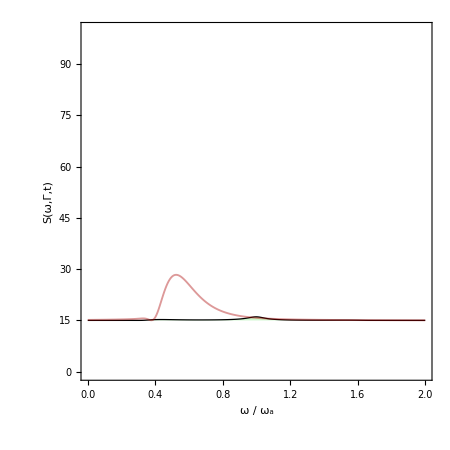

```mathematica
G2 =Show[{ListLinePlot[ParallelTable[{ω,15+S[Γ,ω*ν -ν,-10,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-10",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,15+NumEW2Tanh[Γ,β,ω*ν-ν,T0,-10]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

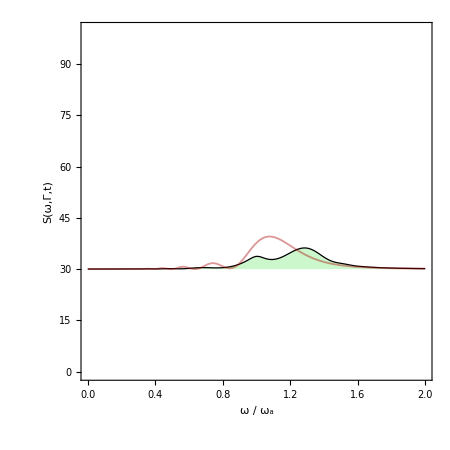

```mathematica
G3 =Show[{ListLinePlot[ParallelTable[{ω,30+S[Γ,ω*ν -ν,10,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,30+NumEW2Tanh[Γ,β,ω*ν-ν,T0,10]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

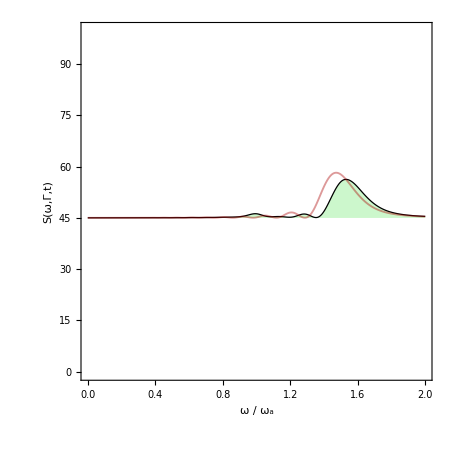

```mathematica
G4 =Show[{ListLinePlot[ParallelTable[{ω,45+S[Γ,ω*ν -ν,30,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Filling->45,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,45+NumEW2Tanh[Γ,β,ω*ν-ν,T0,30]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

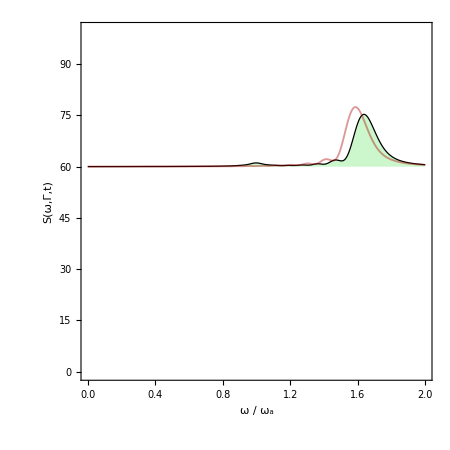

```mathematica
G5 =Show[{ListLinePlot[ParallelTable[{ω,60+S[Γ,ω*ν -ν,50,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Filling->60,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=50",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,60+NumEW2Tanh[Γ,β,ω*ν-ν,T0,50]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

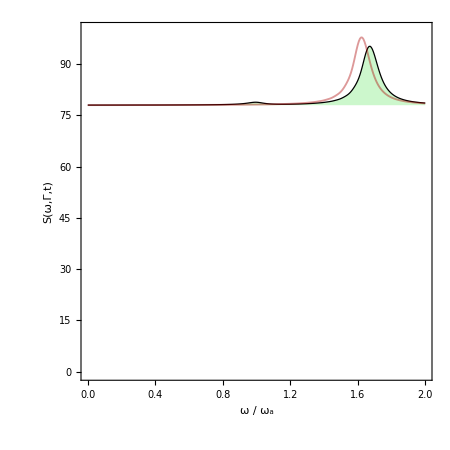

```mathematica
G6 =Show[{ListLinePlot[ParallelTable[{ω,78+S[Γ,ω*ν -ν,90,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Filling->78,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=90",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,78+NumEW2Tanh[Γ,β,ω*ν-ν,T0,90]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,100.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

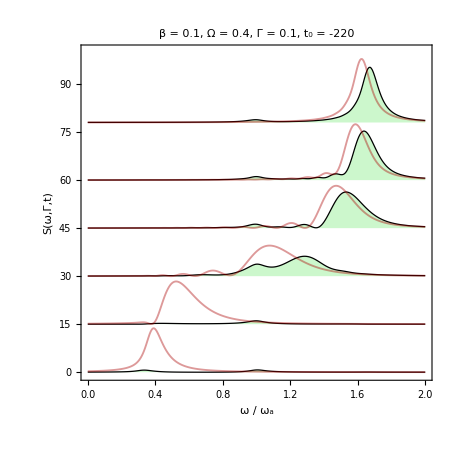

```mathematica
Show[{G6,G5,G4,G3,G2,G1}, PlotLabel-> Style["β = 0.1, Ω = 0.4, Γ = 0.1, t_0 = -220", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/limite_hiperbolico",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/limite_hiperbolico